### B, C, N_critconcept

#### x_C(0)=50, x_D(0)=50, T_s=10

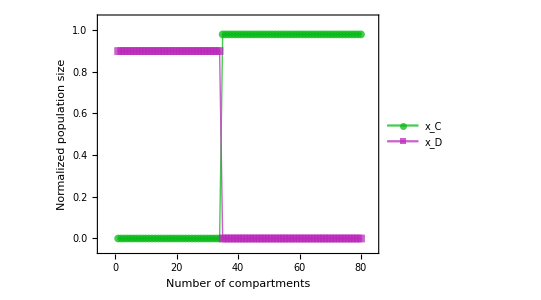

```mathematica
t1=Import [NotebookDirectory[]<>"AllD_AllC_equalpop_Ts_10.txt","Data"];
L1=t1//Length;
ListPlot[{
{t1⟦#⟧⟦1⟧,t1⟦#⟧⟦2⟧}&/@Range[4,L1,1]
,
{t1⟦#⟧⟦1⟧,t1⟦#⟧⟦3⟧}&/@Range[4,L1,1]
}
,Frame->True
,Joined->True
,PlotRange->{80{-0.05,1.05},{-0.05,1.05}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Number of compartments","Normalized population size"}
,PlotStyle->{
{Thick,Opacity[0.75,ColorData["GreenPinkTones"][0.15]]}
,
{Thick,Opacity[0.75,ColorData["GreenPinkTones"][0.85]]}
}
,PlotLegends->{Placed[{"x_C","x_D"},{0.875,0.25}]}
,PlotMarkers->{Automatic,8}
]
```

#### x_C(0)=50, x_D(0)=50, T_s=10, coexistence

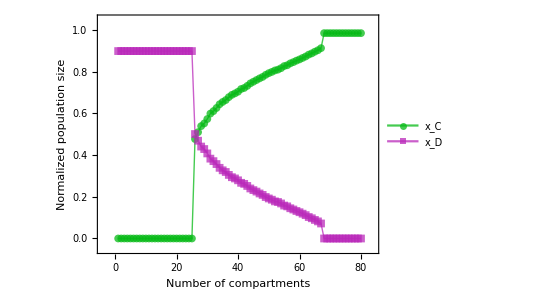

```mathematica
t1=Import [NotebookDirectory[]<>"AllD_coexist_AllC_equalpop_Ts_10.txt","Data"];
L1=t1//Length;
ListPlot[{
{t1⟦#⟧⟦1⟧,t1⟦#⟧⟦2⟧}&/@Range[4,L1,1]
,
{t1⟦#⟧⟦1⟧,t1⟦#⟧⟦3⟧}&/@Range[4,L1,1]
}
,Frame->True
,Joined->True
,PlotRange->{80{-0.05,1.05},{-0.05,1.05}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Number of compartments","Normalized population size"}
,PlotStyle->{
{Thick,Opacity[0.75,ColorData["GreenPinkTones"][0.15]]}
,
{Thick,Opacity[0.75,ColorData["GreenPinkTones"][0.85]]}
}
,PlotLegends->{Placed[{"x_C","x_D"},{0.875,0.25}]}
,PlotMarkers->{Automatic,8}
]
```

### ListDensity (Array) Plot of N_crit

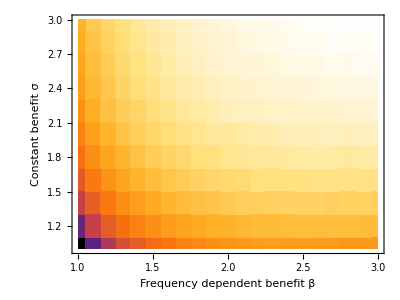

```mathematica
colors="SunsetColors";
FS=20;(*FontSize*)
NcAll=Import [NotebookDirectory[]<>"beta_sigma_Ncrit.txt",{"Data"}];
Nc=NcAll⟦#⟧&/@Range[2,Length[NcAll],1];
Lc=Nc//Length;
ListDensityPlot[
Nc
,Mesh->None
,InterpolationOrder->0
,ColorFunction->ColorData[{colors,"Reverse"}]
,ColorFunctionScaling->True
,Frame->True
,AspectRatio->0.75
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->FS,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.005],Black]
,Axes->{True,False}
,FrameLabel->{"Frequency dependent benefit β","Constant benefit σ"}
]

scale={Min[Nc⟦All,3⟧],Max[Nc⟦All,3⟧]};
BarLegend[
{colors,(*{Min[optimala0D//Flatten],Max[optimala0D//Flatten]}*)scale}
,LegendLabel->"Critical number of compartments N_crit"
,LabelStyle->{FontSize->FS,FontFamily->"Arial",Black}
,LegendLayout->"Row"
,LegendMarkerSize->375
]
```

### D, ListDensity (Array) Plot of N_crit - in powers of 2

#### T_s=10

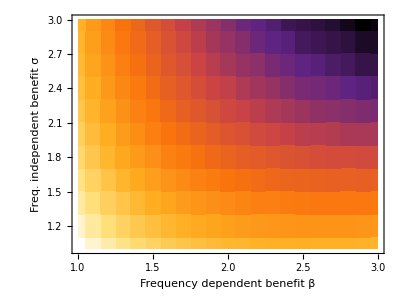

{{1,1,8.58871},{1,1.2,8.30834},{1,1.4,8.07146},{1,1.6,7.88264},{1,1.8,7.72792},{1,2,7.58496},{1,2.2,7.46761},{1,2.4,7.35755},{1,2.6,7.27612},{1,2.8,7.21917},{1,3,7.13955},{1.1,1,8.31741},{1.1,1.2,8.03892},{1.1,1.4,7.82018},{1.1,1.6,7.62936},{1.1,1.8,7.46761},{1.1,2,7.32193},{1.1,2.2,7.19967},{1.1,2.4,7.09803},{1.1,2.6,7.},{1.1,2.8,6.93074},{1.1,3,6.87036},{1.2,1,8.09803},{1.2,1.2,7.82655},{1.2,1.4,7.59991},{1.2,1.6,7.41785},{1.2,1.8,7.2384},{1.2,2,7.09803},{1.2,2.2,6.96578},{1.2,2.4,6.85798},{1.2,2.6,6.76818},{1.2,2.8,6.67243},{1.2,3,6.62936},{1.3,1,7.90689},{1.3,1.2,7.64386},{1.3,1.4,7.42626},{1.3,1.6,7.21917},{1.3,1.8,7.04439},{1.3,2,6.88264},{1.3,2.2,6.75489},{1.3,2.4,6.64386},{1.3,2.6,6.52356},{1.3,2.8,6.44294},{1.3,3,6.37504},{1.4,1,7.74819},{1.4,1.2,7.48382},{1.4,1.4,7.25739},{1.4,1.6,7.05528},{1.4,1.8,6.87036},{1.4,2,6.71425},{1.4,2.2,6.55459},{1.4,2.4,6.45943},{1.4,2.6,6.32193},{1.4,2.8,6.24793},{1.4,3,6.18982},{1.5,1,7.62936},{1.5,1.2,7.36632},{1.5,1.4,7.11894},{1.5,1.6,6.91886},{1.5,1.8,6.72792},{1.5,2,6.53916},{1.5,2.2,6.40939},{1.5,2.4,6.26679},{1.5,2.6,6.14975},{1.5,2.8,6.06609},{1.5,3,5.97728},{1.6,1,7.5157},{1.6,1.2,7.24793},{1.6,1.4,7.},{1.6,1.6,6.78136},{1.6,1.8,6.56986},{1.6,2,6.39232},{1.6,2.2,6.22882},{1.6,2.4,6.08746},{1.6,2.6,5.97728},{1.6,2.8,5.88264},{1.6,3,5.80735},{1.7,1,7.42626},{1.7,1.2,7.14975},{1.7,1.4,6.89482},{1.7,1.6,6.67243},{1.7,1.8,6.45943},{1.7,2,6.26679},{1.7,2.2,6.08746},{1.7,2.4,5.9542},{1.7,2.6,5.83289},{1.7,2.8,5.72792},{1.7,3,5.61471},{1.8,1,7.35755},{1.8,1.2,7.06609},{1.8,1.4,6.80735},{1.8,1.6,6.56986},{1.8,1.8,6.33985},{1.8,2,6.14975},{1.8,2.2,5.97728},{1.8,2.4,5.80735},{1.8,2.6,5.67243},{1.8,2.8,5.55459},{1.8,3,5.45943},{1.9,1,7.29462},{1.9,1.2,7.},{1.9,1.4,6.72792},{1.9,1.6,6.47573},{1.9,1.8,6.22882},{1.9,2,6.04439},{1.9,2.2,5.85798},{1.9,2.4,5.67243},{1.9,2.6,5.52356},{1.9,2.8,5.39232},{1.9,3,5.32193},{2,1,7.2384},{2,1.2,6.94251},{2,1.4,6.67243},{2,1.6,6.39232},{2,1.8,6.14975},{2,2,5.93074},{2,2.2,5.72792},{2,2.4,5.58496},{2,2.6,5.39232},{2,2.8,5.2854},{2,3,5.16993},{2.1,1,7.20945},{2.1,1.2,6.89482},{2.1,1.4,6.59991},{2.1,1.6,6.32193},{2.1,1.8,6.06609},{2.1,2,5.85798},{2.1,2.2,5.64386},{2.1,2.4,5.45943},{2.1,2.6,5.2854},{2.1,2.8,5.16993},{2.1,3,5.},{2.2,1,7.16993},{2.2,1.2,6.85798},{2.2,1.4,6.53916},{2.2,1.6,6.26679},{2.2,1.8,6.02237},{2.2,2,5.75489},{2.2,2.2,5.55459},{2.2,2.4,5.35755},{2.2,2.6,5.20945},{2.2,2.8,5.},{2.2,3,4.90689},{2.3,1,7.14975},{2.3,1.2,6.82018},{2.3,1.4,6.52356},{2.3,1.6,6.20945},{2.3,1.8,5.9542},{2.3,2,5.70044},{2.3,2.2,5.45943},{2.3,2.4,5.2854},{2.3,2.6,5.08746},{2.3,2.8,4.90689},{2.3,3,4.80735},{2.4,1,7.13955},{2.4,1.2,6.80735},{2.4,1.4,6.47573},{2.4,1.6,6.16993},{2.4,1.8,5.90689},{2.4,2,5.61471},{2.4,2.2,5.39232},{2.4,2.4,5.16993},{2.4,2.6,5.},{2.4,2.8,4.85798},{2.4,3,4.64386},{2.5,1,7.12928},{2.5,1.2,6.79442},{2.5,1.4,6.45943},{2.5,1.6,6.14975},{2.5,1.8,5.85798},{2.5,2,5.55459},{2.5,2.2,5.32193},{2.5,2.4,5.08746},{2.5,2.6,4.90689},{2.5,2.8,4.70044},{2.5,3,4.58496},{2.6,1,7.13955},{2.6,1.2,6.79442},{2.6,1.4,6.44294},{2.6,1.6,6.12928},{2.6,1.8,5.80735},{2.6,2,5.52356},{2.6,2.2,5.24793},{2.6,2.4,5.04439},{2.6,2.6,4.85798},{2.6,2.8,4.64386},{2.6,3,4.52356},{2.7,1,7.13955},{2.7,1.2,6.79442},{2.7,1.4,6.44294},{2.7,1.6,6.10852},{2.7,1.8,5.78136},{2.7,2,5.49185},{2.7,2.2,5.20945},{2.7,2.4,5.},{2.7,2.6,4.75489},{2.7,2.8,4.58496},{2.7,3,4.45943},{2.8,1,7.14975},{2.8,1.2,6.79442},{2.8,1.4,6.44294},{2.8,1.6,6.10852},{2.8,1.8,5.78136},{2.8,2,5.42626},{2.8,2.2,5.16993},{2.8,2.4,4.90689},{2.8,2.6,4.70044},{2.8,2.8,4.52356},{2.8,3,4.32193},{2.9,1,7.15987},{2.9,1.2,6.80735},{2.9,1.4,6.44294},{2.9,1.6,6.08746},{2.9,1.8,5.75489},{2.9,2,5.42626},{2.9,2.2,5.12928},{2.9,2.4,4.85798},{2.9,2.6,4.58496},{2.9,2.8,4.39232},{2.9,3,4.16993},{3,1,7.17991},{3,1.2,6.82018},{3,1.4,6.45943},{3,1.6,6.10852},{3,1.8,5.75489},{3,2,5.42626},{3,2.2,5.08746},{3,2.4,4.80735},{3,2.6,4.58496},{3,2.8,4.39232},{3,3,4.24793}}

```mathematica
colors="SunsetColors";
FS=20;(*FontSize*)
NcAll=Import [NotebookDirectory[]<>"beta_sigma_Ncomp_18-Feb-2018_v1.txt","Data"];
Nc={NcAll⟦#,1⟧,NcAll⟦#,2⟧,Log[2,NcAll⟦#,3⟧]//N}&/@Range[4,Length[NcAll],1];
Lc=Nc//Length;

ListDensityPlot[
Nc
,Mesh->None
,InterpolationOrder->0
,ColorFunction->colors(*ColorData[{colors,"Reverse"}]*)
,ColorFunctionScaling->True
,Frame->True
,AspectRatio->0.75
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->FS,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.005],Black]
,Axes->{True,False}
,FrameLabel->{"Frequency dependent benefit β","Freq. independent benefit σ"}
]

scale={Min[Nc⟦All,3⟧],Max[Nc⟦All,3⟧]};
BarLegend[
{colors,scale}
(*,LegendLabel->"Critical number of compartments SubscriptBox[StyleBox[\"N\",FontSlant->\"Italic\"], \"crit\"]"*)
,LabelStyle->{FontSize->FS,FontFamily->"Arial",Black}
,LegendLayout->"Row"
,LegendMarkerSize->375
]

Nc
```

#### T_s=100

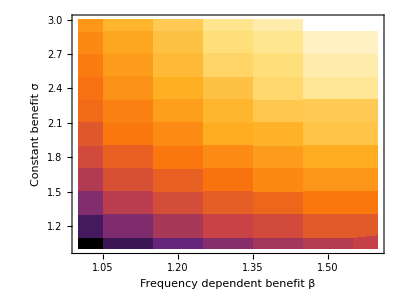

```mathematica
colors="SunsetColors";
FS=20;(*FontSize*)
NcAll=Import [NotebookDirectory[]<>"beta_sigma_Ncomp_19-Feb-2018_v1.txt","Data"];
Nc={NcAll⟦#,1⟧,NcAll⟦#,2⟧,Log[2,NcAll⟦#,3⟧]//N}&/@Range[4,Length[NcAll],1];
Lc=Nc//Length;

ListDensityPlot[
Nc
,Mesh->None
,InterpolationOrder->0
,ColorFunction->ColorData[{colors,"Reverse"}]
,ColorFunctionScaling->True
,Frame->True
,AspectRatio->0.75
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->FS,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.005],Black]
,Axes->{True,False}
,FrameLabel->{"Frequency dependent benefit β","Constant benefit σ"}
]

scale={Min[Nc⟦All,3⟧],Max[Nc⟦All,3⟧]};
BarLegend[
{colors,scale}
(*,LegendLabel->"Critical number of compartments SubscriptBox[StyleBox[\"N\",FontSlant->\"Italic\"], \"crit\"]"*)
,LabelStyle->{FontSize->FS,FontFamily->"Arial",Black}
,LegendLayout->"Row"
,LegendMarkerSize->375
]
```

### E, Hysteresis, T_s=10

200

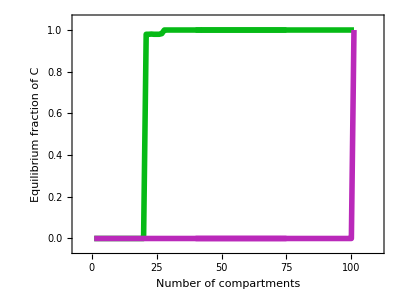

```mathematica
t=Import[NotebookDirectory[]<>"EqualPopHysteresis_Ncomp_Ts_10.txt","Data"];
L=Length[t]-4

c1=Opacity[1,ColorData["GreenPinkTones"][0.15]];
c2=Opacity[1,ColorData["GreenPinkTones"][0.85]];
LP=ListPlot[
{
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[L/2+4,L+4,1],
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[4,L/2+4,1]
}
,Joined->True
,Frame->True
,PlotRange->{105{-0.05,1.05},{-0.05,1.05}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Number of compartments","Equilibrium fraction of C"}
,PlotStyle->{
{Thickness[0.01],c1}
,
{Thickness[0.01],c2}
}
];

a1={Arrowheads[Large],Arrow[{{40,0},{75,0}}]};
a2={Arrowheads[Large],Arrow[{{75,1},{40,1}}]};
Show[
LP,
Graphics[{c2,Thickness[0.01],a1}],
Graphics[{c1,Thickness[0.01],a2}]
]
```

### E, Hysteresis, T_s=100

```mathematica
t=Import[NotebookDirectory[]<>"EqualPopHysteresis_Ncomp_Ts_100.txt","Data"];
L=Length[t]-4

c1=Opacity[1,ColorData["GreenPinkTones"][0.15]];
c2=Opacity[1,ColorData["GreenPinkTones"][0.85]];
LP=ListPlot[
{
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[L/2+4,L+4,1],
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[4,L/2+4,1]
}
,Joined->True
,Frame->True
,PlotRange->{150{-0.05,1.05},{-0.05,1.05}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Number of compartments","Equilibrium fraction of C"}
,PlotStyle->{
{Thickness[0.01],c1}
,
{Thickness[0.01],c2}
}
];

a1={Arrowheads[Large],Arrow[{{40,0},{75,0}}]};
a2={Arrowheads[Large],Arrow[{{75,1},{40,1}}]};
Show[
LP,
Graphics[{c2,Thickness[0.01],a1}],
Graphics[{c1,Thickness[0.01],a2}]
]
```

### E, Hysteresis, T_s=1000

276

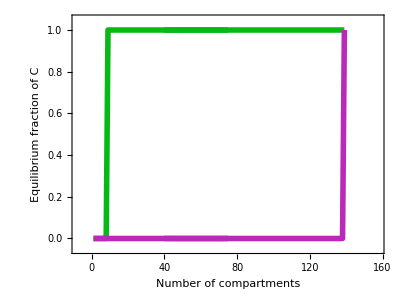

```mathematica
t=Import[NotebookDirectory[]<>"EqualPopHysteresis_Ncomp_Ts_1000.txt","Data"];
L=Length[t]-4

c1=Opacity[1,ColorData["GreenPinkTones"][0.15]];
c2=Opacity[1,ColorData["GreenPinkTones"][0.85]];
LP=ListPlot[
{
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[L/2+4,L+4,1],
{t⟦#,1⟧,t⟦#,2⟧/(t⟦#,2⟧+t⟦#,3⟧)}&/@Range[4,L/2+4,1]
}
,Joined->True
,Frame->True
,PlotRange->{150{-0.05,1.05},{-0.05,1.05}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Number of compartments","Equilibrium fraction of C"}
,PlotStyle->{
{Thickness[0.01],c1}
,
{Thickness[0.01],c2}
}
];

a1={Arrowheads[Large],Arrow[{{40,0},{75,0}}]};
a2={Arrowheads[Large],Arrow[{{75,1},{40,1}}]};
Show[
LP,
Graphics[{c2,Thickness[0.01],a1}],
Graphics[{c1,Thickness[0.01],a2}]
]
```

### F, Analytical (Mean Field)

#### Bottom

{1,2,3,4,5,10,100}

{{1,{}},{2,{}},{3,{}},{4,{}},{5,{}},{10,{}},{100,{}}}

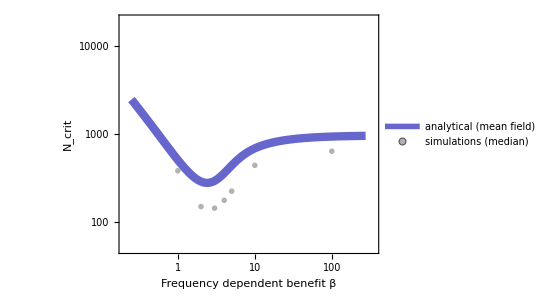

```mathematica
Nc[n_,β_,σ_,δ_,κ_,α_,K_]:=Module[
{f},
f=1/(1+Exp[σ-β])-κ/(α(1+Exp[σ]));


K(1-δ/(α(1+Exp[σ])/(1+Exp[σ-β])-κ))(1-1/β(σ-Log[(1-f)/f]))

]

FTx=If[#<0,(10^#//N),10^#](*{10^#,("10")^ToString[#]}*)&/@Range[-1,3,1];
FTy={10^#,("10")^ToString[#]}&/@Range[2,4,1];
P=LogLogPlot[
Nc[22,β,1.0,0.1,0.5,1.0,1000],{β,0.25,275}
,Frame->True
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{FTy,None},{FTx,None}}
,AspectRatio->0.75
,PlotRange->{{0.2, 3.5 10^2},{50,2 10^4}}
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Frequency dependent benefit β","N_crit"}
,PlotStyle->{
{Thickness[0.015],Opacity[0.6,Darker[Blue]]}
}
,PlotLegends->{Placed[{"analytical (mean field)"},{0.618,0.75}]}
];

NcData=Import[NotebookDirectory[]<>"beta_Ncomp_16-Feb-2018_v1.txt","Data"];

p={NcData⟦#,1⟧,NcData⟦#,2⟧}&/@Range[4,NcData//Length];
Lp=Length[p];
xq=DeleteDuplicates[p⟦All,1⟧]
Lx=Length[xq];
q={xq⟦#⟧,{}}&/@Range[1,Lx,1]

(
AppendTo[q[[Flatten[Position[xq,p⟦#,1⟧]]⟦1⟧,2]],p⟦#,2⟧]
)&/@Range[1,Lp,1];

marker=Graphics[{Gray,Disk[]}];
LP=ListLogLogPlot[
{q⟦#,1⟧,Median[q⟦#,2⟧]}&/@Range[1,Lx,1]
,Frame->True
,PlotRange->{{0.4, 3.5 10^2},{50,2 10^4}}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{FTy,None},{FTx,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0035],Black]
,Axes->{True,False}
,FrameLabel->{"Frequency dependent benefit β","N_crit"}
,PlotStyle->{
{Thickness[0.015],Opacity[0.6,Darker[Blue]]}
}
,PlotMarkers->{marker,0.06}
,PlotLegends->{Placed[{"simulations (median)"},{0.615,0.9}]}
];

Show[P,LP]
```